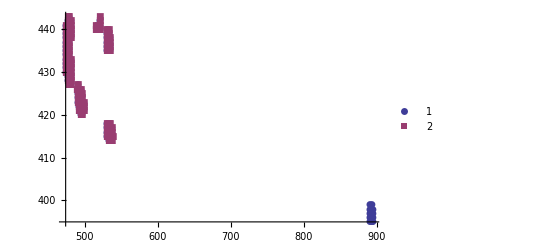

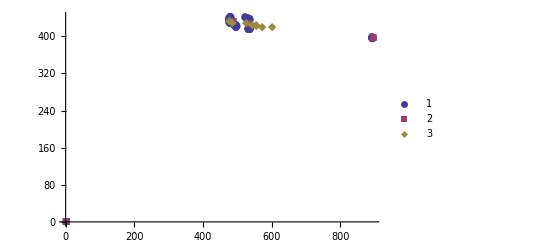

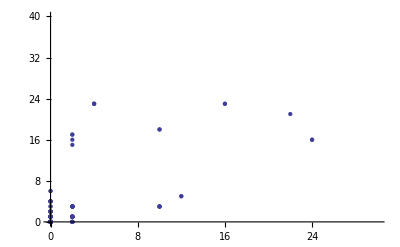

2.37926

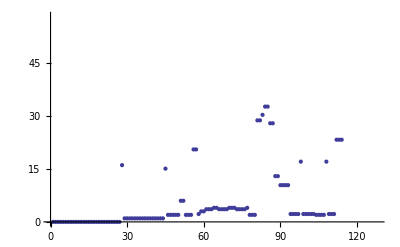

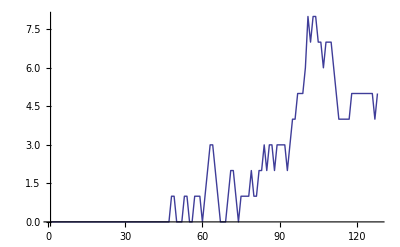

```mathematica
fl1={{478,431},{478,439},{478,432},{478,430},{478,438},{478,440},{476,432},{476,439},{476,438},{476,431},{476,433},{478,433},{476,440},{476,434},{478,441},{478,429},{476,430},{476,437},{478,437},{478,434},{476,441},{494,423},{480,430},{480,431},{494,424},{476,435},{532,416},{494,422},{492,424},{476,429},{480,429},{478,442},{530,437},{496,422},{492,423},{476,436},{532,417},{492,425},{480,432},{532,437},{496,423},{532,436},{480,439},{530,438},{532,438},{892,397},{478,428},{480,440},{496,421},{892,398},{530,416},{530,417},{530,436},{474,438},{892,396},{474,433},{474,434},{474,439},{476,442},{534,416},{494,425},{474,432},{478,435},{490,425},{532,415},{480,438},{494,421},{490,424},{480,428},{532,435},{530,439},{480,441},{490,426},{890,397},{894,397},{532,418},{492,422},{496,424},{478,436},{890,398},{492,426},{474,435},{474,437},{534,437},{534,415},{534,417},{530,435},{894,396},{534,436},{474,440},{496,420},{474,431},{890,396},{894,398},{892,399},{536,416},{530,418},{480,433},{892,395},{534,435},{532,439},{530,415},{536,415},{478,443},{890,399},{474,436},{490,423},{520,441},{534,438},{480,442},{476,428},{498,423},{498,422},{520,442},{890,395},{894,395},{532,414},{494,420},{490,427},{520,440},{530,440},{536,417},{498,421},{494,426},{478,427},{474,430},{534,414},{474,441}};
val1={158,157,154,150,150,149,148,145,144,140,139,138,136,130,129,125,124,122,117,115,115,114,110,110,108,108,106,104,104,103,102,102,101,100,100,100,99,99,99,99,98,98,98,97,97,95,95,95,94,93,93,93,93,93,92,92,92,92,92,91,91,91,91,90,89,88,87,87,87,87,87,87,86,85,85,85,85,85,85,84,84,84,84,84,83,83,83,82,82,82,81,81,80,80,80,80,80,80,79,79,79,78,78,78,77,77,76,76,75,75,74,73,71,71,70,70,70,70,70,70,70,69,68,68,68,68,67,67};
arr1={{486,432},{528,428},{892,397},{0,0},{0,0},{0,0},{0,0},{0,0}};
cp1={{477,435},{484,430},{527,429},{544,425},{572,422},{601,421},{555,426},{554,423}};

fl2={{478,431},{478,439},{478,432},{478,430},{478,438},{478,440},{476,432},{476,439},{476,438},{476,431},{476,433},{478,433},{476,440},{476,434},{478,441},{478,429},{476,430},{476,437},{478,437},{478,434},{476,441},{494,423},{480,430},{480,431},{494,424},{476,435},{532,416},{494,422},{492,424},{476,429},{480,429},{478,442},{530,437},{496,422},{492,423},{476,436},{532,417},{492,425},{480,432},{532,437},{496,423},{532,436},{480,439},{530,438},{532,438},{478,428},{480,440},{496,421},{530,416},{530,417},{530,436},{474,438},{474,433},{474,434},{474,439},{476,442},{534,416},{494,425},{474,432},{478,435},{490,425},{532,415},{480,438},{494,421},{490,424},{480,428},{532,435},{530,439},{480,441},{490,426},{532,418},{492,422},{496,424},{478,436},{492,426},{474,435},{474,437},{534,437},{534,415},{534,417},{530,435},{534,436},{474,440},{496,420},{474,431},{536,416},{530,418},{480,433},{534,435},{532,439},{530,415},{536,415},{478,443},{474,436},{490,423},{520,441},{534,438},{480,442},{476,428},{498,423},{498,422},{520,442},{532,414},{494,420},{490,427},{520,440},{530,440},{536,417},{498,421},{494,426},{478,427},{474,430},{534,414},{474,441},{492,421},{480,427},{476,443},{536,414},{488,426},{518,441},{520,443},{518,440},{534,418},{496,425},{514,440},{532,440},{514,441},{538,415}};
val2={158,157,154,150,150,149,148,145,144,140,139,138,136,130,129,125,124,122,117,115,115,114,110,110,108,108,106,104,104,103,102,102,101,100,100,100,99,99,99,99,98,98,98,97,97,95,95,94,93,93,93,93,92,92,92,92,91,91,91,91,90,89,88,87,87,87,87,87,87,86,85,85,85,85,84,84,84,84,83,83,83,82,82,81,81,80,80,80,79,79,78,78,78,77,76,76,75,75,74,73,71,71,70,70,70,70,70,69,68,68,68,68,67,67,66,66,66,65,65,65,65,64,63,63,63,63,63,62};
arr2={{504,432},{534,416},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}};
cp2={{477,435},{484,430},{503,430},{496,428},{502,428},{509,429},{503,428},{509,430}};

ListPlot[{fl1,fl2}, PlotRange->All,PlotMarkers->Automatic,PlotLegends->Automatic]
ListPlot[{fl1,arr1, cp1}, PlotRange->All,PlotMarkers->Automatic,PlotLegends->Automatic]
fl1 = SortBy[fl1,Last];
fl1 =SortBy[fl1,First];
fl2 = SortBy[fl2,Last];
fl2 =SortBy[fl2,First];
df01 = Abs[fl1-fl2];

ListPlot[df01]
nd12 = Table[N[Norm[fl1⟦i⟧-fl2⟦i⟧]],{i,1, Length[fl1]}];
nn = Length[val1];
(*nn =64;*)
N[StandardDeviation[val1⟦1;;nn⟧-val2⟦1;;nn⟧]]
ListPlot[nd12]
ListLinePlot[{val1- val2}, PlotRange->All, PlotLegends->Automatic]
```

```mathematica
(*fl0={{673,609},{673,606},{673,621},{749,588},{749,615},{697,594},{673,618},{697,597},{693,597},{749,585},{669,609},{753,585},{749,618},{753,582},{693,600},{669,621},{753,615},{669,618},{673,603},{669,612},{909,552},{801,573},{745,588},{669,606},{749,582},{753,588},{905,555},{909,555},{801,576},{673,612},{733,624},{905,552},{797,573},{797,576},{677,603},{677,606},{877,558},{857,564},{673,624},{729,624},{873,561},{701,594},{725,621},{873,558},{877,561},{997,591},{693,594},{829,606},{737,621},{785,576},{745,585},{669,615},{757,582},{689,600},{745,618},{733,627},{969,543},{861,561},{833,567},{837,567},{757,585},{1001,591},{737,624},{949,546},{857,561},{861,564},{781,576},{781,579},{697,591},{701,597},{745,615},{785,579},{997,588},{1001,588},{829,603},{673,615},{753,618},{729,627},{985,540},{969,546},{801,570},{833,606},{749,621},{953,546},{941,549},{837,564},{829,567},{697,600},{689,603},{677,621},{733,621},{745,621},{973,543},{949,549},{905,558},{841,564},{841,567},{753,612},{729,621},{741,621},{981,540},{981,543},{941,546},{937,549},{873,564},{833,570},{761,582},{765,582},{889,600},{681,603},{725,624},{989,540},{945,546},{893,558},{909,558},{865,561},{813,570},{817,570},{829,570},{765,579},{769,579},{833,603},{677,609},{725,618},{953,543},{957,546},{893,555},{845,564}};
fl1={{672,607},{672,610},{672,619},{696,595},{752,586},{672,622},{748,586},{748,616},{696,598},{700,595},{752,583},{752,616},{692,598},{672,604},{676,604},{676,607},{756,586},{748,589},{908,553},{692,601},{904,553},{748,583},{756,583},{800,574},{668,610},{748,619},{700,592},{752,613},{672,616},{904,556},{876,559},{668,619},{732,625},{908,556},{796,574},{696,592},{692,595},{676,622},{700,598},{800,571},{668,607},{872,559},{860,562},{752,589},{724,622},{736,622},{784,577},{800,577},{756,580},{744,586},{996,589},{1000,589},{996,592},{732,622},{728,625},{880,559},{876,562},{780,577},{796,577},{688,601},{828,604},{828,607},{672,613},{676,619},{740,622},{968,544},{972,544},{872,562},{836,565},{832,568},{804,571},{744,589},{680,604},{728,622},{736,625},{856,562},{836,568},{804,574},{1000,592},{668,616},{724,619},{752,619},{668,622},{840,565},{860,565},{752,580},{780,580},{744,619},{952,547},{864,562},{832,565},{856,565},{832,604},{668,613},{756,613},{744,616},{672,625},{972,541},{984,541},{988,541},{956,544},{940,547},{944,547},{948,547},{956,547},{828,568},{840,568},{784,580},{680,601},{832,607},{676,610},{740,619},{980,541},{952,544},{968,547},{940,550},{760,580},{764,580},{760,583},{676,601},{888,601},{676,625},{732,628},{988,538},{936,550},{892,556},{844,565},{796,571}};
fl3={{671,608},{751,587},{695,596},{671,620},{699,596},{699,593},{675,605},{671,611},{675,608},{751,617},{751,584},{755,587},{755,584},{747,587},{695,599},{751,614},{671,605},{671,617},{675,620},{691,599},{695,593},{671,623},{755,581},{903,554},{907,554},{799,575},{675,623},{747,617},{799,572},{803,572},{859,563},{875,560},{879,560},{747,584},{755,614},{803,575},{751,581},{731,623},{675,602},{727,623},{907,551},{999,590},{827,605},{723,620},{879,557},{903,557},{907,557},{995,590},{691,596},{691,602},{679,605},{671,614},{747,614},{739,620},{735,623},{971,545},{783,578},{699,599},{731,626},{971,542},{911,554},{835,566},{839,566},{795,575},{743,587},{679,602},{667,611},{675,617},{739,623},{875,557},{863,563},{831,566},{787,575},{787,578},{747,590},{831,605},{667,608},{747,620},{987,539},{951,545},{955,545},{967,545},{911,551},{859,560},{863,560},{875,563},{831,569},{675,611},{667,620},{751,620},{951,548},{783,575},{779,578},{995,593},{687,602},{827,608},{727,626},{735,626},{939,548},{943,548},{855,563},{835,569},{759,581},{827,602},{723,617},{727,620},{983,542},{987,542},{871,560},{843,566},{827,569},{839,569},{795,572},{759,584},{999,587},{999,593},{687,599},{723,623},{955,548},{891,557},{859,566},{815,569},{799,578},{763,581},{751,590},{783,590},{887,599},{747,602}};
df01 = Abs[fl0-fl1];
df12 = Abs[fl1-fl2];
df02 = Abs[fl0-fl2];
fl0 = SortBy[fl0,Last];
fl0 =SortBy[fl0,First];
fl1 = SortBy[fl1,Last];
fl1 =SortBy[fl1,First];
fl2 = SortBy[fl2,Last];
fl2 =SortBy[fl2,First];
ListPlot[{Abs[fl0-fl1],Abs[fl1-fl2],Abs[fl0-fl2]}, PlotRange->All,PlotMarkers->Automatic,PlotLegends->Automatic]
ListPlot[{df01,df12,df02}, PlotRange->All,PlotMarkers->Automatic,PlotLegends->Automatic]
nd01 = Table[N[Norm[fl0⟦i⟧-fl1⟦i⟧]],{i,1, Length[fl0]}];
nd12 = Table[N[Norm[fl1⟦i⟧-fl2⟦i⟧]],{i,1, Length[fl0]}];
nd02 = Table[N[Norm[fl0⟦i⟧-fl2⟦i⟧]],{i,1, Length[fl0]}];
ListLinePlot[{nd01,nd12,nd02}, PlotRange->All,PlotLegends->Automatic]
nn=16;(*Length[fl0];*)
Variance[nd01⟦1;;nn⟧]
Variance[nd12⟦1;;nn⟧]
Variance[nd02⟦1;;nn⟧]
StandardDeviation[nd01⟦1;;nn⟧]
StandardDeviation[nd12⟦1;;nn⟧]
StandardDeviation[nd02⟦1;;nn⟧]
Length[fl0]*)
```